```mathematica
Select[Keys[stubbornForm],With[{g=stubbornForm[#]["graph"]},
VertexCount[g]==5 &&
EdgeCount[g]==7 &&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,3<->1]&&
EdgeQ[g,4<->1]
]&
]
```

{29413}

```mathematica
Select[Keys[stubbornForm],With[{g=stubbornForm[#]["graph"]},
VertexCount[g]==5 &&
EdgeCount[g]==6 &&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,4<->5]&&
EdgeQ[g,5<->1]&&
EdgeQ[g,3<->1]&&
EdgeQ[g,4<->1]
]&
]
```

{29404}

```mathematica
stubbornForm[29413,"relations"]//Simplify//TableForm
```

x29413+x49204==x9730
x22852==x29413+x35977
x27226==x29413+x31681
x28684==x29413+x30172
x29170==x29413+x29737
x29413==x29494+x29602
x29413==x29440+x29551
x29404==x29413+x29506
x29413==x29416+x29446
x29412==x29413+x29417

```mathematica
ColorTablePrint[29404,stubbornForm,"colofour3","colortable4"]
```

-Graphics-29404s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1Greater
( | = | ≠
1<->2 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1
1<->3 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1
1<->4 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1
1<->5 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1
2<->3 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1
2<->4 | -α1+γ | s12+s17-β1-γ1+δ-δ1+ϵ-ϵ1
2<->5 | s17-β1+δ-δ1 | s12-α1+γ-γ1+ϵ-ϵ1
3<->4 | s12+s17-ζ | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
3<->5 | ϵ-ϵ1 | s12+s17-α1-β1+γ-γ1+δ-δ1
4<->5 | 0 | s12+s17-α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1)

```mathematica
ColorTablePrint[29413,stubbornForm,"colofour","colortable4"]
```

-Graphics-294131/6 (-b01-2 b02-b03-b04-b05+2 b06+2 b08+b09+b10+3 b12+2 b14+2 b15-b19-b20-3 b22-b24-b25+b26+2 b27+b28+b29+b30-2 b31-2 b33-b34-b35+4 b36+b37+4 b38+b39+b40-2 b41-2 b42-2 b43-2 b44-2 b45+2 b46-b47+2 b48+2 ζ)Greater
( | = | ≠
1<->2 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
1<->3 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
1<->4 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
1<->5 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
2<->3 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
2<->4 | -α1+γ | -β1-γ1+δ-δ1+ϵ-ϵ1+ζ
2<->5 | -β1+δ-δ1 | -α1+γ-γ1+ϵ-ϵ1+ζ
3<->4 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ
3<->5 | ϵ-ϵ1 | -α1-β1+γ-γ1+δ-δ1+ζ
4<->5 | 0 | -α1-β1+γ-γ1+δ-δ1+ϵ-ϵ1+ζ)

```mathematica
Select[Keys[stubbornForm],With[{g=stubbornForm[#]["graph"]},
VertexCount[g]==4 &&
EdgeCount[g]==5 &&
EdgeQ[g,1<->2]&&
EdgeQ[g,2<->3]&&
EdgeQ[g,3<->4]&&
EdgeQ[g,4<->1]&&
EdgeQ[g,1<->3] &&
MemberQ[stubbornForm[#]["vertexsets"],{3,4}]
]&
]
```

{29209}

```mathematica
stubbornForm[29209]["vertexsets"]
```

{{1},{2},{5},{3,4}}

```mathematica
Simplify[stubbornForm[29413]["colofour"]-stubbornForm[29209]["colofour"]]
```

1/6 (-b01-b03-b04-3 b05+2 b06+2 b07+3 b09-b10+4 b12+b13+b14+b15-2 b17+b18-2 b19+b20-2 b22-2 b23+b24-2 b25+2 b26+b27+2 b28+2 b29+b30-b31-4 b32-2 b33-2 b34-b35+3 b36+6 b37+3 b38+3 b39-3 b41-3 b43-3 b44-3 b45+3 b46-b47+2 b48-b49-b50+3 ζ)

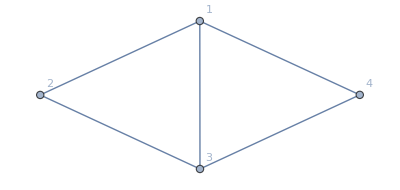

```mathematica
Graph[EdgeList[stubbornForm[29209]["graph"]],VertexLabels->"Name"]
```

```mathematica
Solve[-b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-2 s02-2 s04-2 s05-2 s06-s07-s08-s09-2 s10-s11-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+3 α1-2 β+2 β1-3 γ+3 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+2 ζ==1/6 (-b01-2 b02-b03-b04-b05+2 b06+2 b08+b09+b10+3 b12+2 b14+2 b15-b19-b20-3 b22-b24-b25+b26+2 b27+b28+b29+b30-2 b31-2 b33-b34-b35+4 b36+b37+4 b38+b39+b40-2 b41-2 b42-2 b43-2 b44-2 b45+2 b46-b47+2 b48+2 ζ),b01]
```

{{b01→4 b02+5 b03-b04-7 b05+2 b06+2 b08+b09-5 b10+9 b12+6 b13+2 b14+2 b15-6 b16-6 b17-6 b18-7 b19-b20-3 b22-b24-b25+b26+2 b27+b28+b29+b30-2 b31-2 b33-b34-b35+4 b36+b37+4 b38+b39+b40-2 b41-2 b42-2 b43-2 b44-2 b45+2 b46-b47+2 b48+12 s01+12 s02+12 s04+12 s05+12 s06+6 s07+6 s08+6 s09+12 s10+6 s11+6 s13+6 s14+6 s15+12 s16+12 s17+12 s18+12 s19+12 s20+12 α-18 α1+12 β-12 β1+18 γ-18 γ1+12 δ-12 δ1+12 ϵ-12 ϵ1-10 ζ}}

```mathematica
ColorTablePrint[29506,withRelations,"colofour","colortable"]
```

-Graphics-295061/6 (-v12345-v1234x5+v1235x4+v123x45+v1245x3+v124x35-2 v125x34+v125x3x4-2 v12x345+v12x35x4+v12x3x45-v12x3x4x5-v1345x2+v134x25-v134x2x5+v135x24+v13x245-2 v13x25x4+v13x2x4x5+v145x23+v14x235-2 v14x25x3+v14x2x3x5-2 v15x234+v15x23x4+v15x24x3-v15x2x3x4+v1x234x5-v1x235x4-v1x23x45-v1x245x3-v1x24x35+2 v1x25x34+v1x25x3x4+v1x2x345-v1x2x34x5)Missing[KeyAbsent, comp]
Missing[KeyAbsent,colortable]

```mathematica
DiagGraph[n_]:=Graph[Join[Table[i<->i+1,{i,1,n-1}],Table[i<->0,{i,1,n}]], VertexLabels->"Name",GraphLayout->"CircularEmbedding",VertexSize->Small, VertexStyle->Red]
```

```mathematica
Table[ChromaticPolynomial[DiagGraph[k],x],{k,2,8}]
```

{2 x-3 x^2+x^3,-4 x+8 x^2-5 x^3+x^4,8 x-20 x^2+18 x^3-7 x^4+x^5,-16 x+48 x^2-56 x^3+32 x^4-9 x^5+x^6,32 x-112 x^2+160 x^3-120 x^4+50 x^5-11 x^6+x^7,-64 x+256 x^2-432 x^3+400 x^4-220 x^5+72 x^6-13 x^7+x^8,128 x-576 x^2+1120 x^3-1232 x^4+840 x^5-364 x^6+98 x^7-15 x^8+x^9}

```mathematica
Plot[{2 x-3 x^2+x^3,-4 x+8 x^2-5 x^3+x^4,8 x-20 x^2+18 x^3-7 x^4+x^5,-16 x+48 x^2-56 x^3+32 x^4-9 x^5+x^6,32 x-112 x^2+160 x^3-120 x^4+50 x^5-11 x^6+x^7,-64 x+256 x^2-432 x^3+400 x^4-220 x^5+72 x^6-13 x^7+x^8,128 x-576 x^2+1120 x^3-1232 x^4+840 x^5-364 x^6+98 x^7-15 x^8+x^9},{x,3-0.01,3+0.01, Filling->Bottom}]
```

Plot::plln: Limiting value Filling → Bottom in {x, 3 - 0.01, 3 + 0.01, Filling → Bottom} is not a machine-sized real number.

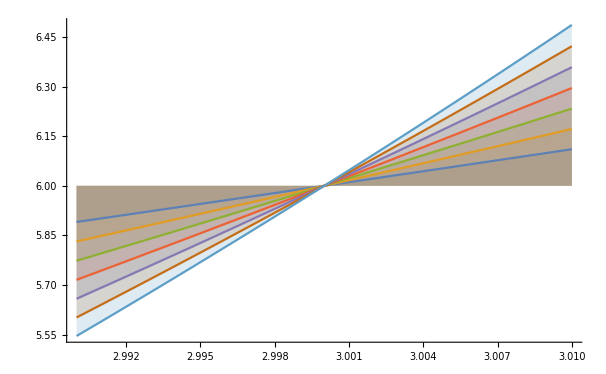

```mathematica
Plot[{2 x-3 x^2+x^3,-4 x+8 x^2-5 x^3+x^4,8 x-20 x^2+18 x^3-7 x^4+x^5,-16 x+48 x^2-56 x^3+32 x^4-9 x^5+x^6,32 x-112 x^2+160 x^3-120 x^4+50 x^5-11 x^6+x^7,-64 x+256 x^2-432 x^3+400 x^4-220 x^5+72 x^6-13 x^7+x^8,128 x-576 x^2+1120 x^3-1232 x^4+840 x^5-364 x^6+98 x^7-15 x^8+x^9},{x,3-0.01,3+0.01},Filling->6]
```

```mathematica
0
```

0

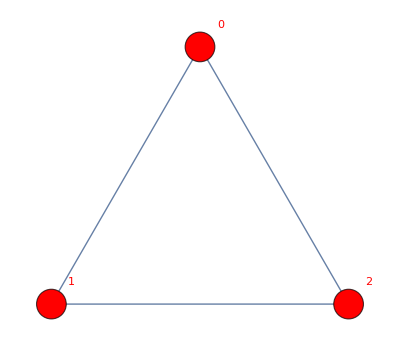
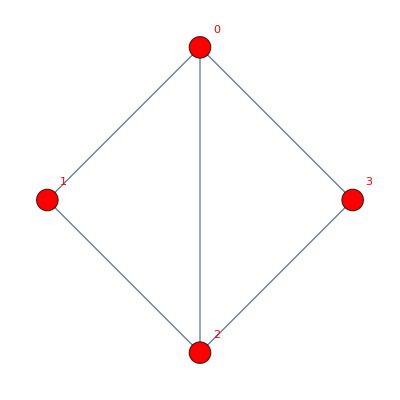
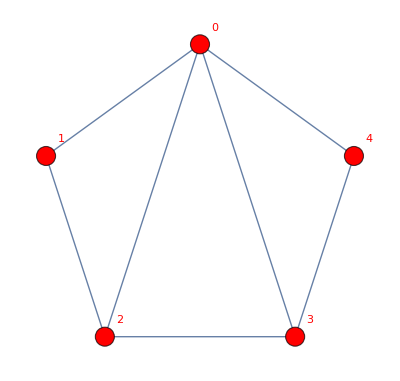
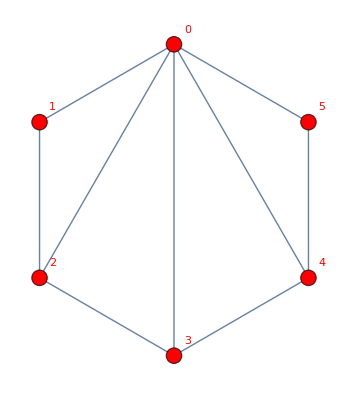
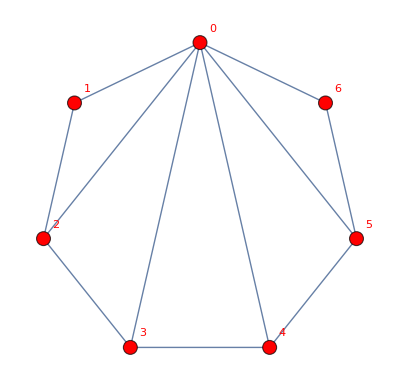
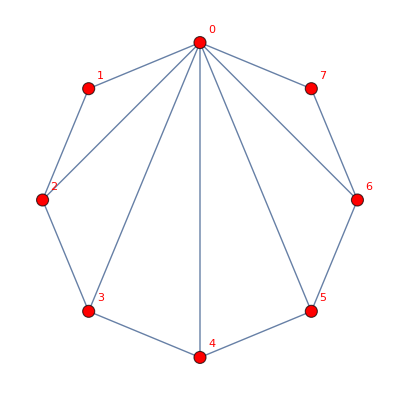
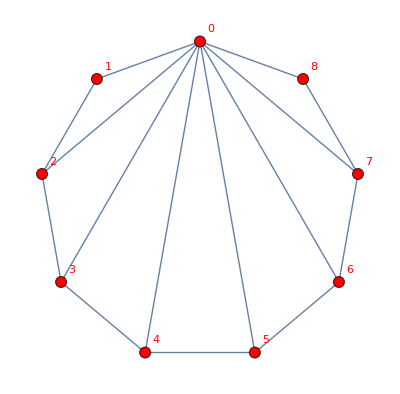
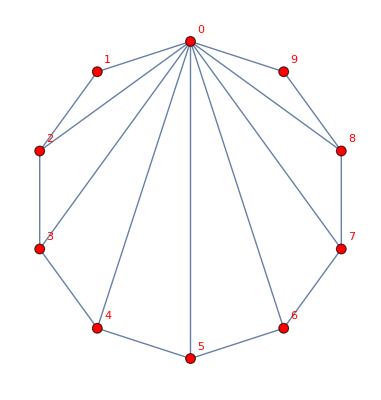
{-Graphics-1,-Graphics--2+x,-Graphics-(-2+x)^2,-Graphics-(-2+x)^3,-Graphics-(-2+x)^4,-Graphics-(-2+x)^5,-Graphics-(-2+x)^6,-Graphics-(-2+x)^7,-Graphics-(-2+x)^8}

```mathematica
Table[With[{g=DiagGraph[k]},Labeled[g,Factor[ChromaticPolynomial[g,x]/((-2+x) (-1+x) x)]]],{k,2,10}]
```

```mathematica
Select[Table[ineqs2[[k]],{k,Length[ineqs2]}],Length[#]<5&]
```

{v1x2x3x4x5>0,v1x2x3x45>0,1802,5 v12345+4 v1234x5+v1235x4+4 v123x45+3 v1245x3+5 v124x3x5+v125x34+v12x345+4 v12x35x4+4 v12x3x4x5+3 v1345x2+5 v134x2x5+5 v135x2x4+v13x24x5+4 v13x25x4+5 v13x2x45+4 v145x23+4 v14x23x5+2 v14x25x3+2 v14x2x35+4 v15x234+5 v15x24x3+5 v15x2x3x4+v1x2345+4 v1x235x4+6 v1x23x4x5+5 v1x245x3+4 v1x24x35+4 v1x25x34+4 v1x2x34x5+5 v1x2x3x45<5 v123x4x5+5 v124x35+4 v125x3x4+5 v12x34x5+7 v12x3x45+5 v134x25+5 v135x24+5 v13x245+5 v13x2x4x5+6 v145x2x3+5 v14x235+4 v14x2x3x5+8 v15x23x4+7 v15x2x34+5 v1x234x5+8 v1x23x45+5 v1x24x3x5+5 v1x25x3x4+4 v1x2x345+5 v1x2x35x4}
 |  |  |  |

```mathematica
Table[ineqs2[[k]],{k,Length[ineqs2]}]
```

{v1x2x3x4x5>0,v1x2x3x45>0,1802,5 v12345+4 v1234x5+v1235x4+4 v123x45+3 v1245x3+5 v124x3x5+v125x34+v12x345+4 v12x35x4+4 v12x3x4x5+3 v1345x2+5 v134x2x5+5 v135x2x4+v13x24x5+4 v13x25x4+5 v13x2x45+4 v145x23+4 v14x23x5+2 v14x25x3+2 v14x2x35+4 v15x234+5 v15x24x3+5 v15x2x3x4+v1x2345+4 v1x235x4+6 v1x23x4x5+5 v1x245x3+4 v1x24x35+4 v1x25x34+4 v1x2x34x5+5 v1x2x3x45<5 v123x4x5+5 v124x35+4 v125x3x4+5 v12x34x5+7 v12x3x45+5 v134x25+5 v135x24+5 v13x245+5 v13x2x4x5+6 v145x2x3+5 v14x235+4 v14x2x3x5+8 v15x23x4+7 v15x2x34+5 v1x234x5+8 v1x23x45+5 v1x24x3x5+5 v1x25x3x4+4 v1x2x345+5 v1x2x35x4}
 |  |  |  |

```mathematica
.
```